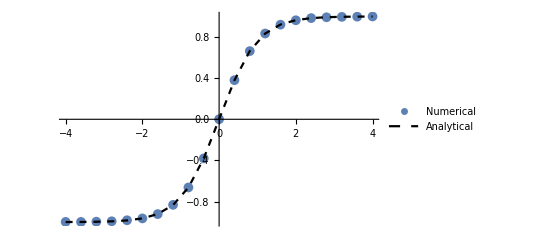

```mathematica
(* We set T = 1. For a given c-bit input I_i, we simulate a single c-bit for 1000 time units and take samples at a high frequency. We plot the average state m_i as a function of I_i. Note that in the code, z is I_i and s is m_i *)

ClearAll["Global`*"];
smean=Flatten@Last@Reap[Do[z=ii; T=1;tsim=1000;
sol=First@NDSolve[{x'[t]==-s[t]+Tanh[z/T],x[0]==0,s[0]==1,WhenEvent[{{x[t]==-1,x[t]==1}},s[t]->Sign[Round[x[t]]]]},{x,s},{t,0,tsim},DiscreteVariables->s];
st=s/.sol;pointsPerTimeStep=2;
svalues=Sow[Mean[st[Range[0.,tsim,1/pointsPerTimeStep]]]];
,{ii,-4,4,0.4}]];
zrange=Range[-4,4,0.4];
numerical=ListPlot[{Transpose[{Range[-4,4,0.4],smean}]},PlotMarkers->{Automatic, Medium},PlotLegends->LineLegend[{"Numerical"}]];
analytical=ListPlot[Transpose[{zrange,Tanh[zrange/T]}],Joined->True,PlotStyle->{Black,Dashed},PlotLegends->LineLegend[{"Analytical"}]];
Show[{numerical,analytical}]
```

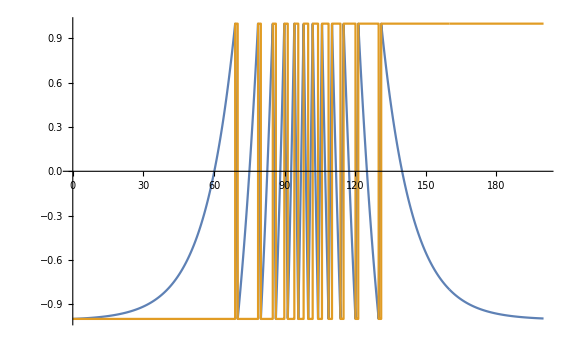

```mathematica
(* We have a single c-bit running for 200 time units, and we sweep the value of I_i from -4 to 4 over that time period. We show the state of the billiard m_i in yellow. *)

tsim=200;
sol=First@NDSolve[{x'[t]==-s[t]+Tanh[8/tsim*t-4],x[0]==-1,s[0]==-1,WhenEvent[x[t]==-1,s[t]->-1],WhenEvent[x[t]==1,s[t]->1]},{x,s},{t,0,tsim},DiscreteVariables->s];

timeValues=Range[0,tsim,0.01];
xtValues=Evaluate[x[t]/. sol]/. t->timeValues;
stValues=Evaluate[s[t]/. sol]/. t->timeValues;

ListLinePlot[{xtValues,stValues},DataRange->{0,tsim},ImageSize->Large]
```